# Chapter. Processing experimental data

In this notebook you are asked to load data from the SERM/Data folder. To prepare for this copy the line below to an input cell, replace the file path with the file path for the "Data" folder on your computer and press ⌤
AppendTo[$Path,”(* path to *)/SERM/Data/chapter15”];
or
AppendTo[$Path,ToFileName[ {NotebookDirectory[],”Data”,”chapter15”}]];

Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
```

```mathematica
SetOptions[EvaluationNotebook[],
PrintingStartingPageNumber->270,

PageHeaders->{
{Cell[TextData[{CounterBox["Page"]}],FontFamily->"Arial",FontSize->12], Cell[TextData[{"Processing experimental data"}],FontFamily->"Arial",FontSize->12],None},
{None,Cell[TextData[CounterBox["Section",CounterFunction:>(Part[{"Introduction","Importing experimental data","Filtering data","Further reading"},#]&)]],FontFamily->"Arial",FontSize->12],Cell[TextData[{CounterBox["Page"]}],FontFamily->"Arial",FontSize->12]}},

PageFooters->{{None,None,None},{None,None,None}},
PrintingOptions-> {
"PrintingMargins"->{{90,90},{60,90}},
"PaperSize"->{596,794},
"PageSize"->{596,794},
"PageHeaderMargins"->{60,60},
"PageFooterMargins"->{30,30},
"GraphicsPrintingFormat"->"DownloadPostScript",
"FirstPageFace"->Right,
"FirstPageHeader"->False,
"FirstPageFooter"->False,
"PrintRegistrationMarks"-> False}];
```

```mathematica
SetOptions[ListPlot,
Axes->False,
BaseStyle->{FontFamily-> "Arial",FontSize-> 10, FontWeight->Plain},
Frame->True,
FrameStyle->{Black,AbsoluteThickness[.5]},
GridLines->None,
ImageSize->288,
PlotStyle->{Black,AbsoluteThickness[.5]},
Joined->True];
```

```mathematica
(* tick function for labelled axes or frames *)
ticks1[min_,max_,steps_,divs_]:=Join[Table[{x,Which[
Chop[x]==0,0,
0<x<2,NumberForm[x,{2,1},NumberPadding->{"","0"}],
x>2,NumberForm[x,{2,0},NumberPadding->{"","0"}],
0>x≥-2,NumberForm[x,{2,1},NumberPadding->{"0","0"}],
-2>x,NumberForm[x,{2,0},NumberPadding->{"","0"}]
],{0.015,0}},{x,min,max,steps}],Table[{x,"",{0.0075,0}},{x,min,max,steps/divs}]];

(* tick function for non-labelled axes or frames *)
ticks2[min_,max_,steps_,divs_]:=Chop[Join[Table[{x,"",{0.015,0}},{x,min,max,steps}],Table[{x,"",{0.0075,0}},{x,min,max,steps/divs}]]];
```

```mathematica
opts={
FrameLabel-> {"E /mV","µA",None,None},
RotateLabel-> False,
PlotRange-> {{-100,600},{-400,300}},
FrameTicks->{ticks1[-100,600,100,5],ticks1[-400,400,200,8],ticks2[-100,600,100,5],ticks2[-400,400,200,8]}};
```

```mathematica
$Line=0;
```

Chapter.Section Introduction

In this final chapter we examine some of the ways to use Mathematica to process experimental data. Commercial equipment makers generally use a variety of file formats for the data generated from experiments but often this data can be converted to a delimited text file. If that is not possible then it is still likely that the data can be imported into Mathematica provided that you understand the formatting structure of your data file. As an example of the use of Mathematica to process experimental data a function to import a comma delimited text file is developed in the next section. In the final section of this chapter some methods of filtering experimental data are explored.

## Chapter.Section Importing experimental data

note

We begin by reading a data file containing experimental data recorded on a Bioanalytical Systems BAS 100B and saved as a comma delimited text file.

```mathematica
dataBAS=Import["500.txt","CSV"];

(* an alternative is to write: dataBAS=Import[SystemDialogInput["FileOpen"],"CSV"] *)
```

Let’s have a look at the first few elements of the list we’ve imported. The data is a mixture of strings and numbers of differing length separated by commas and spaces.

```mathematica
dataBAS⟦1;;60⟧
```

{{Date: 01-May-2003},{Time: 13:03:13},{Label:},{Cyclic Voltammetry},{},{Exp. Conditions:},{Init E (mV) = 550},{High E (mV) = 550},{Low E (mV) = -50},{Init P/N = N},{V (mV/sec) = 200},{Number of Segments = 2},{Sample Interval (mV) = 1},{Quiet Time (sec) = 10},{Sensitivity (A/V) = 1E-4},{},{2 Sets of Data},{Total Number of Data Points = 1200},{##},{Potential (mV),Current (A)},{},{Segment = 1},{Negative},{Number of Data Points = 600},{#},{549.,9.068×10^-6},{548.,0.00001158},{547.,0.0000127},{546.,0.00001325},{545.,0.00001325},{544.,0.00001395},{543.,0.00001395},{542.,0.00001395},{541.,0.00001395},{540.,0.00001465},{539.,0.00001535},{538.,0.00001604},{537.,0.00001674},{536.,0.00001674},{535.,0.00001674},{534.,0.00001604},{533.,0.00001535},{532.,0.00001465},{531.,0.00001465},{530.,0.00001395},{529.,0.00001395},{528.,0.00001395},{527.,0.00001465},{526.,0.00001465},{525.,0.00001465},{524.,0.00001465},{523.,0.00001535},{522.,0.00001535},{521.,0.00001535},{520.,0.00001604},{519.,0.00001604},{518.,0.00001604},{517.,0.00001604},{516.,0.00001535},{515.,0.00001604}}

For the purposes of plotting or manipulating data we are only interested in the sublists containing pairs of numbers. We can select all numeric pairs.

```mathematica
dataBAS2=Cases[dataBAS⟦1;;100⟧,{_?NumberQ,_?NumberQ}]
```

{{549.,9.068×10^-6},{548.,0.00001158},{547.,0.0000127},{546.,0.00001325},{545.,0.00001325},{544.,0.00001395},{543.,0.00001395},{542.,0.00001395},{541.,0.00001395},{540.,0.00001465},{539.,0.00001535},{538.,0.00001604},{537.,0.00001674},{536.,0.00001674},{535.,0.00001674},{534.,0.00001604},{533.,0.00001535},{532.,0.00001465},{531.,0.00001465},{530.,0.00001395},{529.,0.00001395},{528.,0.00001395},{527.,0.00001465},{526.,0.00001465},{525.,0.00001465},{524.,0.00001465},{523.,0.00001535},{522.,0.00001535},{521.,0.00001535},{520.,0.00001604},{519.,0.00001604},{518.,0.00001604},{517.,0.00001604},{516.,0.00001535},{515.,0.00001604},{514.,0.00001604},{513.,0.00001535},{512.,0.00001535},{511.,0.00001535},{510.,0.00001535},{509.,0.00001604},{508.,0.00001535},{507.,0.00001535},{506.,0.00001535},{505.,0.00001535},{504.,0.00001535},{503.,0.00001535},{502.,0.00001395},{501.,0.00001395},{500.,0.00001395},{499.,0.00001395},{498.,0.00001395},{497.,0.00001395},{496.,0.00001395},{495.,0.00001465},{494.,0.00001465},{493.,0.00001465},{492.,0.00001465},{491.,0.00001535},{490.,0.00001535},{489.,0.00001535},{488.,0.00001535},{487.,0.00001535},{486.,0.00001535},{485.,0.00001535},{484.,0.00001465},{483.,0.00001465},{482.,0.00001465},{481.,0.00001535},{480.,0.00001535},{479.,0.00001535},{478.,0.00001535},{477.,0.00001604},{476.,0.00001604},{475.,0.00001604}}

Next step is to examine the elements in the new list. For starters we will look at the first few elements.

```mathematica
FullForm/@Take[dataBAS2,4]
```

{List[549.,9.068×10^-6],List[548.,0.00001158],List[547.,0.0000127],List[546.,0.00001325]}

The experimental data is plotted below:

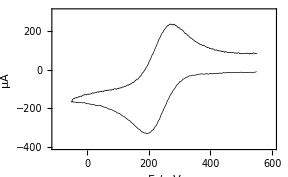

```mathematica
newBASData=Cases[dataBAS,{_?NumberQ,_?NumberQ}];
newBASData⟦All,2⟧=-newBASData⟦All,2⟧*10^6;
mV500Plot=ListPlot[newBASData,opts]
```

Fig. Chapter.FigureCaption  Plot of a cyclic voltammogram recorded on a BAS 100B at a sweep rate of 500 mV · s^-1. Data was saved as a comma delimited file and imported into Mathematica.

These steps can be combined into a function that imports BAS 100B data and plots it.

```mathematica
ClearAll[plotBASdata];

plotBASdata[data_List,opts1___]:=Module[{tmp},
tmp=Cases[data,{_?NumberQ,_?NumberQ}];
tmp⟦All,2⟧=-tmp⟦All,2⟧*10^6;
ListPlot[tmp,opts1]];
```

Another set of data can be imported to test the function.

```mathematica
data2=Import["100.txt","CSV"];
```

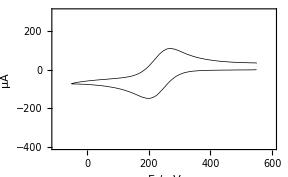

```mathematica
mV100Plot=plotBASdata[data2,opts]
```

Fig. Chapter.FigureCaption  Plot of a cyclic voltammogram recorded on a BAS 100B at a sweep rate of 100 mV · s^-1.

If you have several sets of data you may want to overlay them:

```mathematica
data3=Import["200.txt","CSV"];
data4=Import["20.txt","CSV"];
data5=Import["50.txt","CSV"];
mV200Plot=plotBASdata[data3,opts];
mV20Plot=plotBASdata[data4,opts];
mV50Plot=plotBASdata[data5,opts];
```

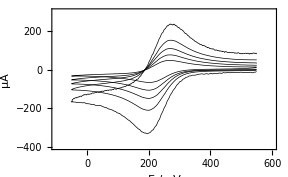

```mathematica
Show[mV20Plot,mV50Plot,mV100Plot,mV200Plot,mV500Plot]
```

Fig. Chapter.FigureCaption  Plots of a cyclic voltammograms recorded on a BAS 100B at a sweep rates of 20, 50, 100, 200 and 500 mV · s^-1.

## Chapter.Section Filtering data

Chapter.Section.Subsection Introduction

In Chapters 7 and 8 a moving average filter was applied to simulated ac voltammetric data to isolate the dc component. The moving average filter could also be used to smooth raw data but better methods exists. In this section we look at three other methods to filter noise from experimental data. To demonstrate the application of the three filters we add some random noise to the cyclic voltammogram from the previous section.

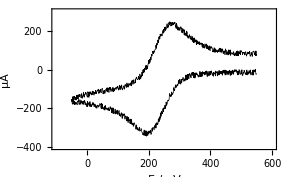

```mathematica
data6=Table[{newBASData⟦i,1⟧,newBASData⟦i,2⟧+Random[Real,{-15.,15.}]},{i,Length[newBASData]}];

ListPlot[data6,opts]
```

Fig. Chapter.FigureCaption  Raw experimental data with random noise added.

### Chapter.Section.Subsection Fourier filter

Data can frequently be filtered using discrete Fourier transforms. Noise is quite often of high frequency and low power and can easily be removed in the frequency domain.

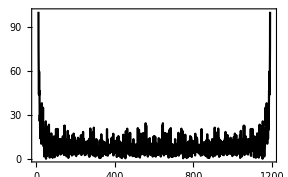

```mathematica
ListPlot[Abs[Fourier[data6⟦All,2⟧]],PlotStyle-> Black,Joined->True,PlotRange->{{0,1200},{0,100}}]
```

The function Chop replaces numbers less than a certain threshold with zero. The default value is 10^-10. A simple filtering procedure is to chop any element in the Fourier transformed data whose absolute value is less than a certain threshold. In the step below all data with values less than 25 are set to zero.

```mathematica
filteredData=Chop[Fourier[data6⟦All,2⟧],25];
```

Here is a plot of the Fourier transformed data after applying Chop.

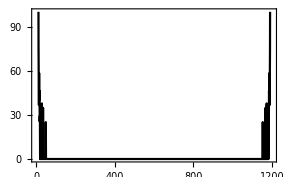

```mathematica
ListPlot[Abs[filteredData],PlotStyle-> Black,Joined->True,PlotRange->{{0,1200},{0,100}}]
```

Performing the inverse Fourier transform on the filtered data converts it back to the time domain.

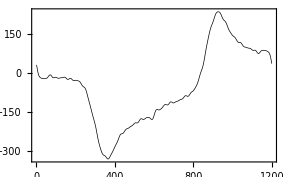

```mathematica
data8=Chop[InverseFourier[filteredData]];
data9=Transpose[{First[Transpose[newBASData]],data8}];ListPlot[data8,Joined-> True]
```

Fig. 17.FigureCaption  Data filtered by chopping out high frequency components in the frequency domain.

### Chapter.Section.Subsection Convolution filter

Convolutions are used extensively in smoothing data. The Fourier transformed signal can be convolved with a suitable response function centred at t=0. In this example a Gaussian function is convolved with the Fourier transformed noisy data.

```mathematica
ClearAll[len,filter];
len=30;
filter=Table[Exp[-x^2/100.],{x,-len,len}];
```

This list contains data with a maximum in the centre. The convolution theorem requires the signal and response lists to have the same lengths. This can be accomplished by padding the filter with zeros.

```mathematica
ClearAll[len2,len3]

len2=Length[data6⟦All,2⟧];
len3=len2+2*len;
filter=PadLeft[filter,len3,0,len2/2];
```

The filter can be centred at t=0 by rotating it to the left. The filter must also be normalized.

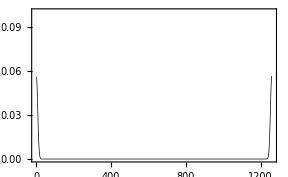

```mathematica
(*Tr works faster than Plus@@filter*)
filter=RotateLeft[filter,len+len2/2]/Tr[filter];
ListPlot[filter,PlotRange-> {0,.1}]
```

The convolution requires the signal to be periodic and since it is not this can lead to some unwanted data at the ends of the filtered result. To avoid this the signal list is padded with zeros.

```mathematica
ClearAll[signal]
signal=PadRight[data6⟦All,2⟧,Length[data6⟦All,2⟧]+2*len];
```

The discrete Fourier transforms of the signal and filter are then multiplied and the inverse transformation made.

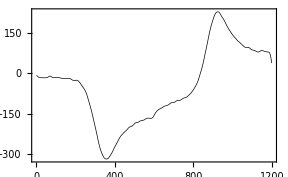

```mathematica
ClearAll[conv];

conv=InverseFourier[Sqrt[len2]*Chop[Fourier[signal]]*Fourier[filter]];
conv=Drop[conv,-(2*len)];

ListPlot[conv]
```

Fig. 17.FigureCaption  Data filtered by convolution with a Gaussian kernel.

The filtered data can be compared to the original data.

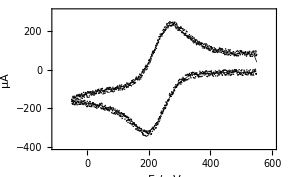

```mathematica
data9=Transpose[{First[Transpose[newBASData]],conv}];

ListPlot[data9,opts,Prolog-> {AbsolutePointSize[1.],Point/@data6}]
```

Fig. 17.FigureCaption  Comparison between data filtered by convolution with a Gaussian kernel and raw experimental data with random noise added.

The Mathematica function ListConvolve performs a convolution on lists without the requirement for the filter (kernel) to be a list of the same length as the raw data (signal). We can repeat the convolution with ListConvolve using a Gaussian filter as the kernel.

```mathematica
ClearAll[filter2,conv2];
len=30;
filter2=Table[Exp[-n^2/100.],{n,-len,len}];
filter2=filter2/(Plus@@filter2);

conv2=ListConvolve[filter2,signal,{-1-len,1+len}];
conv2=Drop[conv2,-(2*len)];
```

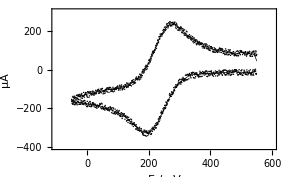

```mathematica
data9=Transpose[{First[Transpose[newBASData]],conv2}];ListPlot[data9,opts,Prolog-> {AbsolutePointSize[1.],Point/@data6}]
```

Fig. 17.FigureCaption  Comparison between data filtered using the function ListConvolve with a Gaussian kernel and raw experimental data with random noise added.

### Chapter.Section.Subsection Savitzky Golay filter

The final filter is a Savitzky-Golay filter. The coefficients for the Savitzky-Golay filtering can be generated with the built-in function SavitzkyGolayMatrix.

```mathematica
Clear[coeffs];
coeffs=SavitzkyGolayMatrix[{20},1]
```

{0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902}

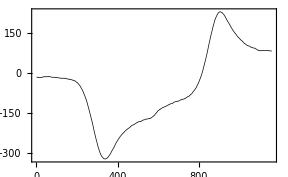

```mathematica
Clear[sgFilter]
sgFilter=Map[coeffs . # &, Partition[data6⟦All,2⟧, Length[coeffs], 1]];
ListPlot[sgFilter]
```

Fig. 17.FigureCaption  Savitzky-Golay filtered data.

The Savitzky-Golay filter reduces the length of the list.

```mathematica
diff=Length[First[Transpose[newBASData]]]-Length[sgFilter]
```

40

The x axis potential scale can be added back after chopping the ends of the raw data.

```mathematica
xAxis=Drop[Drop[First[Transpose[newBASData]],-diff/2],diff/2];
```

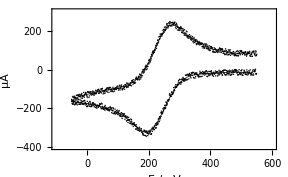

```mathematica
data9=Transpose[{xAxis,sgFilter}];ListPlot[data9,opts,Prolog-> {AbsolutePointSize[1.],Black,Point/@data6}]
```

Fig. 17.FigureCaption  Comparison between Savitzky-Golay filtered data and raw experimental data with random noise added.

## Further reading

Press, W. H., Teukolsky, S. A., Vetterling, W. T., and Flannery, B. P. (1992). Numerical Recipes in C, (2nd edn). Cambridge University Press, New York
Riddle, A. and Stein, D. (1997). Mathematica in the Laboratory, Cambridge University Press, New York.